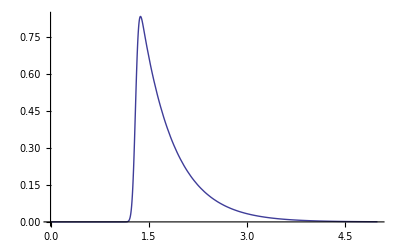

```mathematica
a=4*^-2;
inpoisson={1.3};
epoisson[t_]:=Sum[1/(√(2π) a) Exp[-(t-inpoisson[[k]])^2/(2 a^2)],{k,1,Length[inpoisson]}]
ns=NDSolve[{
y'[t]==-2 y[t]+epoisson[t],
y[0]==0},y[t],{t,0,5}];
Plot[Evaluate[y[t]/.ns[[1]]],{t,0,5},PlotRange->All]
```

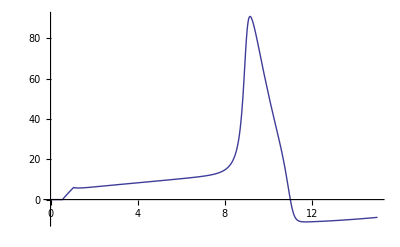

```mathematica
cap=1;
Vna=115;
Vk=-12;
Vl=10.6;
Gna=120;
Gk=36;
Gl=0.3;
T=15;
I1ext[t_]:=2.3*HeavisideTheta[t-0.1];
I1ext[t_]:=13.279*HeavisidePi[2 (t-0.8)];
fan[v_]:=(0.1-0.01 v)/(Exp[1-0.1 v]-1)
fam[v_]:=(2.5-0.1 v)/(Exp[2.5-0.1 v]-1)
fah[v_]:=0.07 Exp[-v/20]
fbn[v_]:=0.125 Exp[-v/80]
fbm[v_]:=4 Exp[-v/18]
fbh[v_]:=1/(Exp[3-0.1 v]+1)
ns=NDSolve[{
cap*V1'[t]==-(V1[t]-Vna) Gna h1[t] m1[t]^3-(V1[t]-Vk) Gk n1[t]^4-(V1[t]-Vl) Gl+I1ext[t],
m1'[t]==(1-m1[t]) fam[V1[t]]-m1[t] fbm[V1[t]],
h1'[t]==(1-h1[t]) fah[V1[t]]-h1[t] fbh[V1[t]],
n1'[t]==(1-n1[t]) fan[V1[t]]-n1[t] fbn[V1[t]],
V1[0]==0,
m1[0]==0.05293248525724958,
h1[0]==0.5961207535084603,
n1[0]==0.3176769140606974
},{V1,m1,h1,n1},{t,0,T}];
Plot[Evaluate[V1[t]/.ns[[1]]],{t,0,T},PlotRange->All]
```

```mathematica
FindMaximum[{Evaluate[V1[t]/.ns[[1]]],7<t<10},{t,9}]
```

{90.8999,{t→9.15478}}

```mathematica
FindMinimum[{Evaluate[V1[t]/.ns[[1]]],10<t<12},{t,11}]
```

{-11.0725,{t→11.6997}}

```mathematica
(* I=2.3 *)
99.410
-10.865
(* 13.279*HeavisidePi[2 (t-0.8)]; *)
90.899
-11.072
```

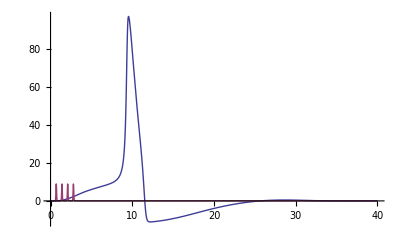

```mathematica
cap=1;
Vna=115;
Vk=-12;
Vl=10.6;
Gna=120;
Gk=36;
Gl=0.3;
sde=0.5;
sre=3.0;
sdi=0.5;
sri=7.0;
Vge=65;
Vgi=-15;
a=4*^-2;
fe=0.04;
fi=0.04;
T=40;
inpoisson={1.0};
inpoisson=Table[0.7 k,{k,1,4}];
pie[t_]:=Sum[1/(√(2π) a) Exp[-(t-inpoisson[[k]])^2/(2 a^2)],{k,1,Length[inpoisson]}]
pii[t_]:=0

fan[v_]:=(0.1-0.01 v)/(Exp[1-0.1 v]-1)
fam[v_]:=(2.5-0.1 v)/(Exp[2.5-0.1 v]-1)
fah[v_]:=0.07 Exp[-v/20]
fbn[v_]:=0.125 Exp[-v/80]
fbm[v_]:=4 Exp[-v/18]
fbh[v_]:=1/(Exp[3-0.1 v]+1)
ns=NDSolve[{
cap*V1'[t]==-(V1[t]-Vna) Gna h1[t] m1[t]^3-(V1[t]-Vk) Gk n1[t]^4-(V1[t]-Vl) Gl+I1[t],
m1'[t]==(1-m1[t]) fam[V1[t]]-m1[t] fbm[V1[t]],
h1'[t]==(1-h1[t]) fah[V1[t]]-h1[t] fbh[V1[t]],
n1'[t]==(1-n1[t]) fan[V1[t]]-n1[t] fbn[V1[t]],
I1[t]==I1e[t]+I1i[t],
I1e[t]==-(V1[t]-Vge) G1e[t],
I1i[t]==-(V1[t]-Vgi) G1i[t],
G1e'[t]==-G1e[t]/sde+H1e[t],
H1e'[t]==-H1e[t]/sre+fe*pie[t],
G1i'[t]==-G1i[t]/sdi+H1i[t],
H1i'[t]==-H1i[t]/sri+fi*pii[t],
V1[0]==0,
m1[0]==0.05293248525724958,
h1[0]==0.5961207535084603,
n1[0]==0.3176769140606974,
G1e[0]==0,
H1e[0]==0,
G1i[0]==0,
H1i[0]==0
},{V1,m1,h1,n1,I1,I1e,I1i,G1e,H1e,G1i,H1i},{t,0,T}];
Plot[{Evaluate[V1[t]/.ns[[1]]],0.9*pie[t]},{t,0,T},PlotRange->All]
```

```mathematica
Solve[(1-x) fan[v0]-x fbn[v0]==0/.v0->0,x]
```

{{x→0.317677}}

```mathematica
FindMaximum[{Evaluate[V1[t]/.ns[[1]]],1<t<4},{t,3}]
```

{1.23799,{t→3.01309}}

```mathematica
FindMaximum[{Evaluate[V1[t]/.ns[[1]]],2<t<8},{t,4}]
```

{1.23776,{t→4.01317}}

```mathematica
stv=0.5;
tb=Table[Evaluate[V1[stv j]/.ns[[1]]],{j,0,80}];
```

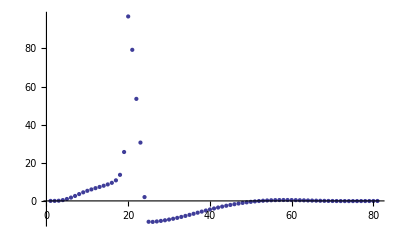

```mathematica
ListPlot[tb,PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"tb.txt",tb]
```

/home/xyy/matcode/prj_GC_clean/HH/tb.txt